```mathematica
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX["pdfLaTeX" -> "/usr/local/bin/pdflatex"];
```

```mathematica
Needs["MaTeX`"]
```

## Cogging Torque

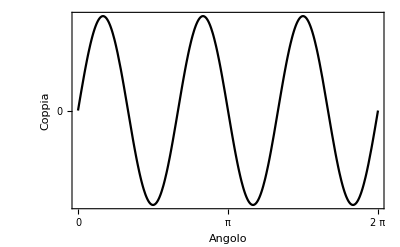

```mathematica
coggingTorque = Plot[Sin[3*x], {x, 0, 2Pi},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{Placed[LineLegend[{MaTeX[TeXForm[Subscript[τ, c]],Magnification->2]}], {.85, .9}]},
PlotRange->{5, -5},
FrameLabel ->{"Angolo", "Coppia"},
FrameTicks->{{{0}, None}, {{0, Pi, 2Pi}, None}},
GridLines->{{0, Pi, 2Pi}, {0}}
]
```

```mathematica
Export["../cogging-torque.pdf",coggingTorque,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/cogging-torque.pdf